## Bose-Hubbard model simulation

References:
	F. Verstraete, V. Murg, J. I. Cirac
	Matrix product states, projected entangled pair states, and variational renormalization group methods for quantum spin systems
	Advances in Physics 57, 143-224 (2008) DOI

	Thomas Barthel
	Precise evaluation of thermal response functions by optimized density matrix renormalization group schemes
	New Journal of Physics 15, 073010 (2013) DOI

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
SparseIdentityMatrix[d_]:=SparseArray[{i_,i_}->1,{d,d}]
```

```mathematica
SiteCreateOp[M_]:=DiagonalMatrix[Sqrt[Range[1,M]],-1]
SiteAnnihilOp[M_]:=DiagonalMatrix[Sqrt[Range[1,M]],1]
```

```mathematica
NumberOp[M_]:=DiagonalMatrix[Range[0,M]]
```

```mathematica
(* construct Bose-Hamiltonian with open boundary conditions *)
Subscript[H, bose][t_,U_,μ_,M_,1]:=U/2 NumberOp[M].(NumberOp[M]-IdentityMatrix[M+1])-μ NumberOp[M]
Subscript[H, bose][t_,U_,μ_,M_,L_]:=-t Sum[KroneckerProduct[SparseIdentityMatrix[(M+1)^(l-1)],SiteCreateOp[M],SiteAnnihilOp[M],SparseIdentityMatrix[(M+1)^(L-l-1)]]+KroneckerProduct[SparseIdentityMatrix[(M+1)^(l-1)],SiteAnnihilOp[M],SiteCreateOp[M],SparseIdentityMatrix[(M+1)^(L-l-1)]],{l,1,L-1}]+Sum[KroneckerProduct[SparseIdentityMatrix[(M+1)^(l-1)],U/2 NumberOp[M].(NumberOp[M]-IdentityMatrix[M+1])-μ NumberOp[M],SparseIdentityMatrix[(M+1)^(L-l)]],{l,1,L}]
```

### Simulation parameters

```mathematica
(* kinetic hopping parameter *)
Subscript[tH, val]=1;
```

```mathematica
(* interaction strength *)
Subscript[U, val]=5;
```

```mathematica
(* chemical potential *)
Subscript[μ, val]=1/7;
```

```mathematica
(* number of lattice sites *)
Subscript[L, val]=5;
```

```mathematica
(* single site occupation number cut-off *)
Subscript[M, val]=2;
```

```mathematica
(* inverse temperature *)
Subscript[β, val]=3/5;
```

```mathematica
Subscript[t, list]=Range[0,5,1/8];
Length[%]
```

41

### Out-of-time-order correlations

```mathematica
OTOC[A_,B_,C_,D_,H_,β_,t_]:=Module[{expβH=MatrixExp[-β H],At=MatrixExp[-ⅈ t H].A.MatrixExp[ⅈ t H],Ct=MatrixExp[-ⅈ t H].C.MatrixExp[ⅈ t H]},Tr[expβH.At.B.Ct.D]/Tr[expβH]]
```

```mathematica
GF[A_,B_,H_,β_,t_]:=Module[{expβH=MatrixExp[-β H],At=MatrixExp[-ⅈ t H].A.MatrixExp[ⅈ t H]},Tr[expβH.At.B]/Tr[expβH]]
```

```mathematica
SiteAverage[A_,H_,β_]:=Module[{expβH=MatrixExp[-β H]},Tr[expβH.A]/Tr[expβH]]
```

```mathematica
SiteCreateOpFull[j_,M_,L_]:=KroneckerProduct[SparseIdentityMatrix[(M+1)^j],SiteCreateOp[M],SparseIdentityMatrix[(M+1)^(L-j-1)]]
```

```mathematica
SiteAnnihilOpFull[j_,M_,L_]:=KroneckerProduct[SparseIdentityMatrix[(M+1)^j],SiteAnnihilOp[M],SparseIdentityMatrix[(M+1)^(L-j-1)]]
```

```mathematica
SiteNumberOpFull[j_,M_,L_]:=KroneckerProduct[SparseIdentityMatrix[(M+1)^j],NumberOp[M],SparseIdentityMatrix[(M+1)^(L-j-1)]]
```

```mathematica
Subscript[fn, import]="../output/bose_hubbard/L"<>ToString[Subscript[L, val]]<>"_otoc/bose_hubbard_L"<>ToString[Subscript[L, val]]<>"_M"<>ToString[Subscript[M, val]];
```

```mathematica
(* read simulation results from disk *)
```

```mathematica
Subscript[density, list]=Import[Subscript[fn, import]<>"_density.dat","Real64"]
Dimensions[%]
```

{0.621552,0.675377,0.67607,0.675414,0.621585}

{5}

```mathematica
Subscript[otoc1, list]=First[#]+ⅈ Last[#]&/@Partition[Import[Subscript[fn, import]<>"_otoc1.dat","Real64"],2]
Dimensions[%]
```

{0.455157+0. ⅈ,0.454541-5.56059×10^-6 ⅈ,0.45209-0.000229505 ⅈ,0.446467-0.00146723 ⅈ,0.436317-0.00447577 ⅈ,0.420174-0.00885424 ⅈ,0.395993-0.0132077 ⅈ,0.361811-0.0168429 ⅈ,0.317661-0.0210176 ⅈ,0.266765-0.0281265 ⅈ,0.214428-0.039722 ⅈ,0.165556-0.0555622 ⅈ,0.123249-0.0745381 ⅈ,0.0896335-0.096051 ⅈ,0.0673852-0.119817 ⅈ,0.0592699-0.144169 ⅈ,0.0654518-0.16529 ⅈ,0.0815645-0.179172 ⅈ,0.100466-0.184786 ⅈ,0.116666-0.184784 ⅈ,0.128936-0.182468 ⅈ,0.138242-0.178333 ⅈ,0.143465-0.170216 ⅈ,0.139996-0.156593 ⅈ,0.122988-0.138815 ⅈ,0.0919807-0.11956 ⅈ,0.0521115-0.0994026 ⅈ,0.0108303-0.076014 ⅈ,-0.026287-0.0472115 ⅈ,-0.0573131-0.0139713 ⅈ,-0.083391+0.0198222 ⅈ,-0.107171+0.0497654 ⅈ,-0.131292+0.0725255 ⅈ,-0.157304+0.0853688 ⅈ,-0.184748+0.0852335 ⅈ,-0.210483+0.0698261 ⅈ,-0.229418+0.0406943 ⅈ,-0.237394+0.00487868 ⅈ,-0.234113-0.0278437 ⅈ,-0.222707-0.0500407 ⅈ,-0.206539-0.0588238 ⅈ}

{41}

```mathematica
Subscript[otoc2, list]=First[#]+ⅈ Last[#]&/@Partition[Import[Subscript[fn, import]<>"_otoc2.dat","Real64"],2]
Dimensions[%]
```

{0.99838+0. ⅈ,0.999211+0.0000778852 ⅈ,1.00453+0.00363907 ⅈ,1.01533+0.0250458 ⅈ,1.01662+0.0841944 ⅈ,0.975255+0.184989 ⅈ,0.861221+0.298035 ⅈ,0.678743+0.371817 ⅈ,0.474936+0.370871 ⅈ,0.309621+0.306355 ⅈ,0.211299+0.226218 ⅈ,0.161786+0.173499 ⅈ,0.122207+0.153632 ⅈ,0.0729584+0.138838 ⅈ,0.0312881+0.10196 ⅈ,0.0309093+0.0481874 ⅈ,0.082029+0.0131879 ⅈ,0.154236+0.0275408 ⅈ,0.201702+0.0871774 ⅈ,0.199331+0.159237 ⅈ,0.155949+0.206868 ⅈ,0.10566+0.211002 ⅈ,0.0847852+0.183779 ⅈ,0.102676+0.162024 ⅈ,0.130301+0.177723 ⅈ,0.118922+0.228836 ⅈ,0.03508+0.271395 ⅈ,-0.103312+0.240232 ⅈ,-0.214839+0.105471 ⅈ,-0.211461-0.0701384 ⅈ,-0.0994744-0.164082 ⅈ,0.00727892-0.120554 ⅈ,0.0104941-0.013742 ⅈ,-0.0692828+0.0481893 ⅈ,-0.144883+0.0433592 ⅈ,-0.174219+0.0237637 ⅈ,-0.177541+0.0269158 ⅈ,-0.181532+0.0460447 ⅈ,-0.189757+0.0606854 ⅈ,-0.192235+0.0624977 ⅈ,-0.183153+0.0589975 ⅈ}

{41}

```mathematica
Subscript[gf, list]=First[#]+ⅈ Last[#]&/@Partition[Import[Subscript[fn, import]<>"_gf.dat","Real64"],2]
Dimensions[%]
```

{0.171286+0. ⅈ,0.171023-0.000543716 ⅈ,0.170073-0.00118786 ⅈ,0.167989-0.00184841 ⅈ,0.164153-0.00209302 ⅈ,0.158076-0.00110623 ⅈ,0.149742+0.0020738 ⅈ,0.139764+0.00811057 ⅈ,0.129183+0.0169614 ⅈ,0.119+0.0277982 ⅈ,0.109801+0.0393136 ⅈ,0.101686+0.0502046 ⅈ,0.094553+0.0595081 ⅈ,0.0884262+0.0666269 ⅈ,0.0835622+0.0711396 ⅈ,0.0802496+0.0726304 ⅈ,0.078489+0.0707225 ⅈ,0.0778153+0.0653108 ⅈ,0.0773906+0.0568084 ⅈ,0.0762805+0.0461929 ⅈ,0.0737112+0.0347858 ⅈ,0.0691877+0.0238926 ⅈ,0.0625079+0.0145089 ⅈ,0.053769+0.00719441 ⅈ,0.0433808+0.00208838 ⅈ,0.0320173-0.000998852 ⅈ,0.0204719-0.00243613 ⅈ,0.00948645-0.00257729 ⅈ,-0.000319754-0.00158516 ⅈ,-0.00837239+0.000623469 ⅈ,-0.0140004+0.00424412 ⅈ,-0.0164188+0.00930304 ⅈ,-0.0149793+0.0153908 ⅈ,-0.00962403+0.0216124 ⅈ,-0.00124192+0.0268341 ⅈ,0.00839631+0.0300859 ⅈ,0.0171767+0.0308632 ⅈ,0.0233468+0.029172 ⅈ,0.0259591+0.0253842 ⅈ,0.0248571+0.0200793 ⅈ,0.0203628+0.0139691 ⅈ}

{41}

```mathematica
Subscript[i, site]=1;
Subscript[j, site]=3;
```

```mathematica
(* reference calculation *)
```

```mathematica
Block[{tH=Subscript[tH, val],U=Subscript[U, val],μ=Subscript[μ, val],M=Subscript[M, val],L=Subscript[L, val],β=Subscript[β, val],HB},HB=N[Subscript[H, bose][tH,U,μ,M,L]];Subscript[density, list,ref]=Table[SiteAverage[SiteNumberOpFull[i,M,L],HB,β],{i,0,L-1}]]
```

{0.621553,0.675362,0.676021,0.675362,0.621553}

```mathematica
Block[{tH=Subscript[tH, val],U=Subscript[U, val],μ=Subscript[μ, val],M=Subscript[M, val],L=Subscript[L, val],β=Subscript[β, val],HB},HB=N[Subscript[H, bose][tH,U,μ,M,L]];Subscript[otoc1, list,ref]=Table[OTOC[SiteCreateOpFull[Subscript[j, site],M,L],SiteCreateOpFull[Subscript[i, site],M,L],SiteAnnihilOpFull[Subscript[j, site],M,L],SiteAnnihilOpFull[Subscript[i, site],M,L],HB,β,t],{t,Subscript[t, list]}]]
```

{0.45511,0.454491-4.44271×10^-6 ⅈ,0.452034-0.000226561 ⅈ,0.446406-0.00145934 ⅈ,0.436259-0.00445984 ⅈ,0.420126-0.00883005 ⅈ,0.395957-0.0131796 ⅈ,0.361788-0.0168166 ⅈ,0.317648-0.0209949 ⅈ,0.266761-0.0281067 ⅈ,0.214431-0.0397053 ⅈ,0.165572-0.055551 ⅈ,0.123279-0.0745352 ⅈ,0.0896724-0.0960569 ⅈ,0.0674216-0.119831 ⅈ,0.0592933-0.144192 ⅈ,0.0654607-0.165321 ⅈ,0.0815647-0.179209 ⅈ,0.100464-0.184822 ⅈ,0.116662-0.184813 ⅈ,0.12893-0.182484 ⅈ,0.138235-0.178334 ⅈ,0.143459-0.170203 ⅈ,0.139992-0.156573 ⅈ,0.122987-0.138796 ⅈ,0.0919784-0.119548 ⅈ,0.0521047-0.0993973 ⅈ,0.0108197-0.0760142 ⅈ,-0.0262979-0.0472167 ⅈ,-0.0573213-0.0139816 ⅈ,-0.0833976+0.0198078 ⅈ,-0.107181+0.0497491 ⅈ,-0.131308+0.0725087 ⅈ,-0.157324+0.0853534 ⅈ,-0.184766+0.0852209 ⅈ,-0.210495+0.0698159 ⅈ,-0.229425+0.0406864 ⅈ,-0.2374+0.00487546 ⅈ,-0.234119-0.027841 ⅈ,-0.222714-0.0500363 ⅈ,-0.206542-0.0588235 ⅈ}

```mathematica
Block[{tH=Subscript[tH, val],U=Subscript[U, val],μ=Subscript[μ, val],M=Subscript[M, val],L=Subscript[L, val],β=Subscript[β, val],HB},HB=N[Subscript[H, bose][tH,U,μ,M,L]];Subscript[otoc2, list,ref]=Table[OTOC[SiteCreateOpFull[Subscript[j, site],M,L],SiteAnnihilOpFull[Subscript[i, site],M,L],SiteAnnihilOpFull[Subscript[j, site],M,L],SiteCreateOpFull[Subscript[i, site],M,L],HB,β,t],{t,Subscript[t, list]}]]
```

{0.998291,0.999122+0.0000739927 ⅈ,1.00445+0.00363562 ⅈ,1.01525+0.0250364 ⅈ,1.01655+0.084178 ⅈ,0.975198+0.184963 ⅈ,0.861174+0.298002 ⅈ,0.678704+0.371784 ⅈ,0.474912+0.370842 ⅈ,0.309617+0.30633 ⅈ,0.211314+0.226202 ⅈ,0.161814+0.173499 ⅈ,0.12224+0.153649 ⅈ,0.0729877+0.13887 ⅈ,0.0313095+0.102001 ⅈ,0.0309219+0.048234 ⅈ,0.0820357+0.0132379 ⅈ,0.154242+0.027591 ⅈ,0.201711+0.0872236 ⅈ,0.199344+0.159274 ⅈ,0.155968+0.206895 ⅈ,0.10569+0.211024 ⅈ,0.084822+0.183804 ⅈ,0.102712+0.16205 ⅈ,0.130334+0.177746 ⅈ,0.118954+0.228859 ⅈ,0.0351068+0.27142 ⅈ,-0.103298+0.240258 ⅈ,-0.214838+0.105491 ⅈ,-0.211468-0.0701244 ⅈ,-0.0994843-0.164072 ⅈ,0.007271-0.120545 ⅈ,0.0104891-0.013726 ⅈ,-0.0692918+0.048217 ⅈ,-0.144903+0.0433915 ⅈ,-0.174247+0.0237897 ⅈ,-0.17757+0.0269301 ⅈ,-0.181558+0.0460468 ⅈ,-0.189776+0.0606774 ⅈ,-0.192247+0.0624845 ⅈ,-0.18316+0.058985 ⅈ}

```mathematica
Block[{tH=Subscript[tH, val],U=Subscript[U, val],μ=Subscript[μ, val],M=Subscript[M, val],L=Subscript[L, val],β=Subscript[β, val],HB},HB=N[Subscript[H, bose][tH,U,μ,M,L]];Subscript[gf, list,ref]=Table[GF[SiteCreateOpFull[Subscript[j, site],M,L],SiteAnnihilOpFull[Subscript[i, site],M,L],HB,β,t],{t,Subscript[t, list]}]]
```

{0.171317,0.171048-0.000553907 ⅈ,0.170086-0.00120298 ⅈ,0.167988-0.00186138 ⅈ,0.164143-0.00209826 ⅈ,0.158065-0.00110434 ⅈ,0.149733+0.00208122 ⅈ,0.139759+0.00812245 ⅈ,0.12918+0.0169769 ⅈ,0.119002+0.0278147 ⅈ,0.109805+0.0393296 ⅈ,0.101693+0.0502198 ⅈ,0.0945631+0.0595218 ⅈ,0.088439+0.0666371 ⅈ,0.0835745+0.0711443 ⅈ,0.0802574+0.0726292 ⅈ,0.0784896+0.0707172 ⅈ,0.0778079+0.0653045 ⅈ,0.0773768+0.0568045 ⅈ,0.0762627+0.0461937 ⅈ,0.0736914+0.0347917 ⅈ,0.0691668+0.0239037 ⅈ,0.0624873+0.014525 ⅈ,0.0537506+0.00721429 ⅈ,0.0433661+0.00210966 ⅈ,0.0320073-0.000978085 ⅈ,0.0204678-0.0024174 ⅈ,0.00948907-0.00256314 ⅈ,-0.000312474-0.0015789 ⅈ,-0.00836559+0.000620275 ⅈ,-0.0139995+0.0042337 ⅈ,-0.0164259+0.00929047 ⅈ,-0.0149919+0.0153808 ⅈ,-0.00963676+0.0216064 ⅈ,-0.0012503+0.0268291 ⅈ,0.00839267+0.0300772 ⅈ,0.0171742+0.0308484 ⅈ,0.0233405+0.0291529 ⅈ,0.0259469+0.0253655 ⅈ,0.0248407+0.0200659 ⅈ,0.0203465+0.0139629 ⅈ}

```mathematica
(* compare *)
Abs[Subscript[density, list]-Subscript[density, list,ref]]
```

{9.09636×10^-7,0.0000148271,0.0000489787,0.0000516645,0.0000314596}

```mathematica
(* compare *)
Norm[Subscript[otoc1, list]-Subscript[otoc1, list,ref],∞]
```

0.0000618532

```mathematica
(* compare *)
Norm[Subscript[otoc2, list]-Subscript[otoc2, list,ref],∞]
```

0.0000890692

```mathematica
(* compare *)
Norm[Subscript[gf, list]-Subscript[gf, list,ref],∞]
```

0.0000306323

```mathematica
Subscript[plot, label]="Bose-Hubbard model with\nt_H="<>ToString[Subscript[tH, val]]<>", U="<>ToString[Subscript[U, val]]<>", μ="<>ToString[InputForm[Subscript[μ, val]]]<>", M="<>ToString[Subscript[M, val]]<>", L="<>ToString[Subscript[L, val]]<>", β="<>ToString[N[Subscript[β, val]]]<>"\nsites: i="<>ToString[Subscript[i, site]]<>", j="<>ToString[Subscript[j, site]];
```

```mathematica
Subscript[fn, export]="plots/"<>#<>"/"<>#<>"_"&[FileBaseName[NotebookFileName[]]];
```

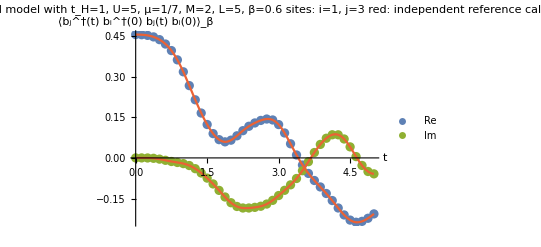

```mathematica
Show[ListPlot[{Transpose[{Subscript[t, list],Re[Subscript[otoc1, list]]}],Transpose[{Subscript[t, list],Im[Subscript[otoc1, list]]}]},AxesLabel->{"t","⟨b_j^†(t) b_i^†(0) b_j(t) b_i(0)⟩_β"},PlotLabel->Subscript[plot, label]<>"\nred: independent reference calculation",PlotStyle->{ColorData[97][1],ColorData[97][3]},PlotLegends->{"Re","Im"}],Plot[{Interpolation[Transpose[{Subscript[t, list],Re[Subscript[otoc1, list,ref]]}]][τ],Interpolation[Transpose[{Subscript[t, list],Im[Subscript[otoc1, list,ref]]}]][τ]},{τ,0,5},PlotRange->All,PlotStyle->ColorData[97][4]]]
Export[Subscript[fn, export]<>"otoc1_L"<>ToString[Subscript[L, val]]<>".pdf",%];
```

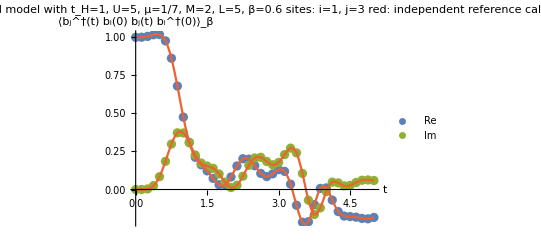

```mathematica
Show[ListPlot[{Transpose[{Subscript[t, list],Re[Subscript[otoc2, list]]}],Transpose[{Subscript[t, list],Im[Subscript[otoc2, list]]}]},AxesLabel->{"t","⟨b_j^†(t) b_i(0) b_j(t) b_i^†(0)⟩_β"},PlotLabel->Subscript[plot, label]<>"\nred: independent reference calculation",PlotStyle->{ColorData[97][1],ColorData[97][3]},PlotLegends->{"Re","Im"}],Plot[{Interpolation[Transpose[{Subscript[t, list],Re[Subscript[otoc2, list,ref]]}]][τ],Interpolation[Transpose[{Subscript[t, list],Im[Subscript[otoc2, list,ref]]}]][τ]},{τ,0,5},PlotRange->All,PlotStyle->ColorData[97][4]]]
Export[Subscript[fn, export]<>"otoc2_L"<>ToString[Subscript[L, val]]<>".pdf",%];
```

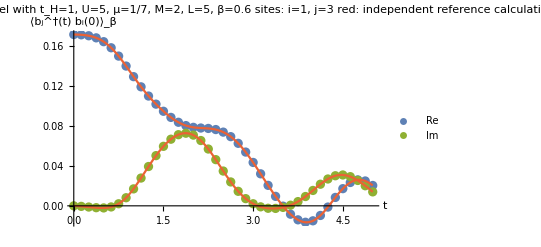

```mathematica
Show[ListPlot[{Transpose[{Subscript[t, list],Re[Subscript[gf, list]]}],Transpose[{Subscript[t, list],Im[Subscript[gf, list]]}]},AxesLabel->{"t","⟨b_j^†(t) b_i(0)⟩_β"},PlotLabel->Subscript[plot, label]<>"\nred: independent reference calculation",PlotStyle->{ColorData[97][1],ColorData[97][3]},PlotLegends->{"Re","Im"}],Plot[{Interpolation[Transpose[{Subscript[t, list],Re[Subscript[gf, list,ref]]}]][τ],Interpolation[Transpose[{Subscript[t, list],Im[Subscript[gf, list,ref]]}]][τ]},{τ,0,5},PlotRange->All,PlotStyle->ColorData[97][4]]]
Export[Subscript[fn, export]<>"gf_L"<>ToString[Subscript[L, val]]<>".pdf",%];
```

### Virtual bond dimensions

```mathematica
Subscript[t, plot]={0,1/2,1,2,4,5};
```

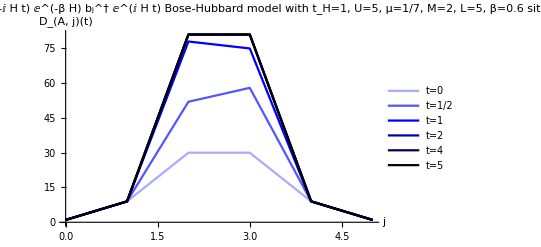

```mathematica
(* virtual bond dimension for 'A' operator *)
Partition[Import[Subscript[fn, import]<>"_DXA.dat","Integer64"],Subscript[L, val]+1];
%⟦#⟧&/@Flatten[Position[Subscript[t, list],#]&/@Subscript[t, plot]];
ListLinePlot[Transpose[{Range[0,Subscript[L, val]],#}]&/@%,AxesLabel->{"j","D_(A, j)(t)"},PlotRange->All,PlotLabel->"virtual bond dimension of ⅇ^(-ⅈ H t) ⅇ^(-β H) b_j^† ⅇ^(ⅈ H t)\n"<>Subscript[plot, label],PlotStyle->{Lighter[Blue,2/3],Lighter[Blue,1/3],Blue,Darker[Blue,1/3],Darker[Blue,2/3],Black},PlotLegends->("t="<>ToString[InputForm[#]]&/@Subscript[t, plot])]
Export[Subscript[fn, export]<>"DA_L"<>ToString[Subscript[L, val]]<>"_M"<>ToString[Subscript[M, val]]<>".pdf",%];
```

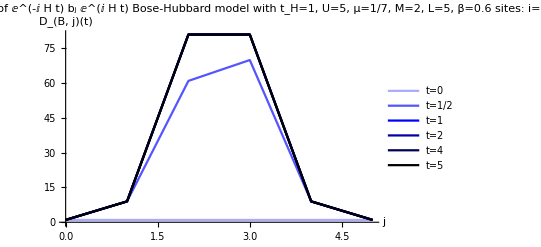

```mathematica
(* virtual bond dimension for 'B' operator *)
Partition[Import[Subscript[fn, import]<>"_DXB.dat","Integer64"],Subscript[L, val]+1];
%⟦#⟧&/@Flatten[Position[Subscript[t, list],#]&/@Subscript[t, plot]];
ListLinePlot[Transpose[{Range[0,Subscript[L, val]],#}]&/@%,AxesLabel->{"j","D_(B, j)(t)"},PlotRange->All,PlotLabel->"virtual bond dimension of ⅇ^(-ⅈ H t) b_j ⅇ^(ⅈ H t)\n"<>Subscript[plot, label],PlotStyle->{Lighter[Blue,2/3],Lighter[Blue,1/3],Blue,Darker[Blue,1/3],Darker[Blue,2/3],Black},PlotLegends->("t="<>ToString[InputForm[#]]&/@Subscript[t, plot])]
Export[Subscript[fn, export]<>"DB_L"<>ToString[Subscript[L, val]]<>"_M"<>ToString[Subscript[M, val]]<>".pdf",%];
```

### Effective truncation weight

```mathematica
(* tolerance (truncation weight) for ⅇ^(-β H) *)
Partition[Import[Subscript[fn, import]<>"_tol_eff_beta.dat","Real64"],Subscript[L, val]-1]
```

{{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10}}

```mathematica
(* tolerance (truncation weight) for ⅇ^(-ⅈ H t) ⅇ^(-β H) Subscript[b, j]^† ⅇ^(ⅈ H t) *)
Partition[Import[Subscript[fn, import]<>"_tol_eff_A.dat","Real64"],Subscript[L, val]-1]
Dimensions[%]
```

{{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10}}

{40,4}

```mathematica
(* tolerance (truncation weight) for ⅇ^(-ⅈ H t) Subscript[b, j] ⅇ^(ⅈ H t) *)
Partition[Import[Subscript[fn, import]<>"_tol_eff_B.dat","Real64"],Subscript[L, val]-1]
Dimensions[%]
```

{{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10}}

{40,4}